#### Polytropic interpolation for G2 EoS

```mathematica
dheavy={{0,0,0},{0.18,0.00110637,0.000123486},{0.2,0.00151811,0.000111776},{0.22,0.00208304,0.000079017},{0.24,0.00309918,0.000144038},{0.26,0.00429562,0.000260806},{0.28,0.00387751,0.000195464},{0.3,0.00786396,0.000404354},{0.32,0.0137287,0.000650502},{0.34,0.0197046,0.000598608},{0.36,0.0243828,0.000372009},{0.4,0.0271982,0.000182171},{0.42,0.0264943,0.000181594},{0.44,0.0274103,0.000173365},{0.48,0.0273374,0.000204433},{0.5,0.0295112,0.000382481},{0.5,0.0308065,0.000260144},{0.52,0.0352139,0.000335109},{0.54,0.0352143,0.000894907},{0.56,0.0374233,0.000881497},{0.6,0.0537042,0.000975687},{0.7,0.106987,0.00046004},{0.8,0.202169,0.000862469},{0.9,0.359465,0.00151906},{1.,0.693259,0.0012576},{1.1,1.5767,0.00192981},{1.2,3.22497,0.00198903},{1.3,5.51716,0.00143838},{1.4,8.44217,0.00112608},{1.5,11.5558,0.00174252},{1.6,13.6381,0.00275352}};
(**,{1.7,13.9944,0.000736476},{1.8,14.0011,0.000458305},{1.9,14.0019,0.000562317},{2.,14.0011,0.000318698})) cs>1**)
```

```mathematica
hbarc = 197.32698;(**MeVfm**)
alat  = 0.357 ;(**fm**)
amn = 1.7;(**a**)
amn/alat*hbarc
```

939.652

```mathematica
μ= dheavy[[All,1]]*3/amn
n=dheavy[[All,2]]/(3*amn^3) 
μ[[20]]
μ[[21]]
```

{0.,0.317647,0.352941,0.388235,0.423529,0.458824,0.494118,0.529412,0.564706,0.6,0.635294,0.705882,0.741176,0.776471,0.847059,0.882353,0.882353,0.917647,0.952941,0.988235,1.05882,1.23529,1.41176,1.58824,1.76471,1.94118,2.11765,2.29412,2.47059,2.64706,2.82353}

{0.,0.0000750641,0.000103,0.000141328,0.000210271,0.000291446,0.000263078,0.000533548,0.000931454,0.0013369,0.0016543,0.00184532,0.00179756,0.00185971,0.00185477,0.00200225,0.00209014,0.00238916,0.00238919,0.00253907,0.00364368,0.00725877,0.0137166,0.0243887,0.0470357,0.106975,0.218805,0.374324,0.572778,0.784029,0.925307}

0.988235

1.05882

```mathematica
(**Length[latdat]
nsat = latdat[[38,2]];
μsat = latdat[[38,1]];**)
μarr=μ[[21;;]]
narr = n[[21;;]]
```

{1.05882,1.23529,1.41176,1.58824,1.76471,1.94118,2.11765,2.29412,2.47059,2.64706,2.82353}

{0.00364368,0.00725877,0.0137166,0.0243887,0.0470357,0.106975,0.218805,0.374324,0.572778,0.784029,0.925307}

```mathematica
μPP[n_, c_, Γ_, K_]:=c+Γ*K*n^(Γ-1)/(Γ-1)
PPP[n_, Γ_, K_]:=K*n^Γ
epsPP[n_,c_,Γ_,K_]:=c*n+K*n^Γ/(Γ-1)
csPP[n_,c_,Γ_,K_]:=(Γ*PPP[n, Γ, K])/(PPP[n, Γ, K]+epsPP[n,c, Γ, K])
```

```mathematica
(**nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=NSolve[0==(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,Γ]**)
nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=Γ/.FindRoot[(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,{Γ,1.5},PrecisionGoal->6]
nextK[n0_,Γ1_,P0_]:=n0^-Γ1 P0
nextc[μ1_,n1_,K1_,Γ1_]:=μ1-(K1 n1^(-1+Γ1) Γ1)/(Γ1-1)
nextP[n1_,Γ1_,K1_]:=K1 n1^Γ1
```

```mathematica
Γ00=5/3//N;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
epsarr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
epsarr[[1]]=epsPP[narr[[1]],carr[[1]],Γarr[[1]],Karr[[1]]];
```

```mathematica
For[i=2,i<Length[narr]+1,i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
epsarr[[i]]=epsPP[narr[[i]],carr[[i]],Γarr[[i]],Karr[[i]]];
]
```

```mathematica
μarr
narr;
Parr;
carr
Karr
Γarr
Parr
Export[NotebookDirectory[]<>"output/cKgP_DM_heavy.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

{1.05882,1.23529,1.41176,1.58824,1.76471,1.94118,2.11765,2.29412,2.47059,2.64706,2.82353}

{1,1.02662,0.794993,0.511901,-5.28021,3.45469,-4.61186,0.978164,1.27397,1.57363,1.98112}

{0.99369,96088.6,2.07026,0.81115,0.294825,0.173821,0.25494,0.362161,0.402283,0.44896,0.55167}

{1.66667,3.71116,1.52961,1.31115,1.03863,0.865782,1.03713,1.26816,1.37508,1.57208,2.41881}

{0.0000857336,0.00110659,0.00292917,0.00622956,0.0123229,0.0250998,0.0527216,0.104162,0.186957,0.306259,0.457227}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/cKgP_DM_heavy.csv

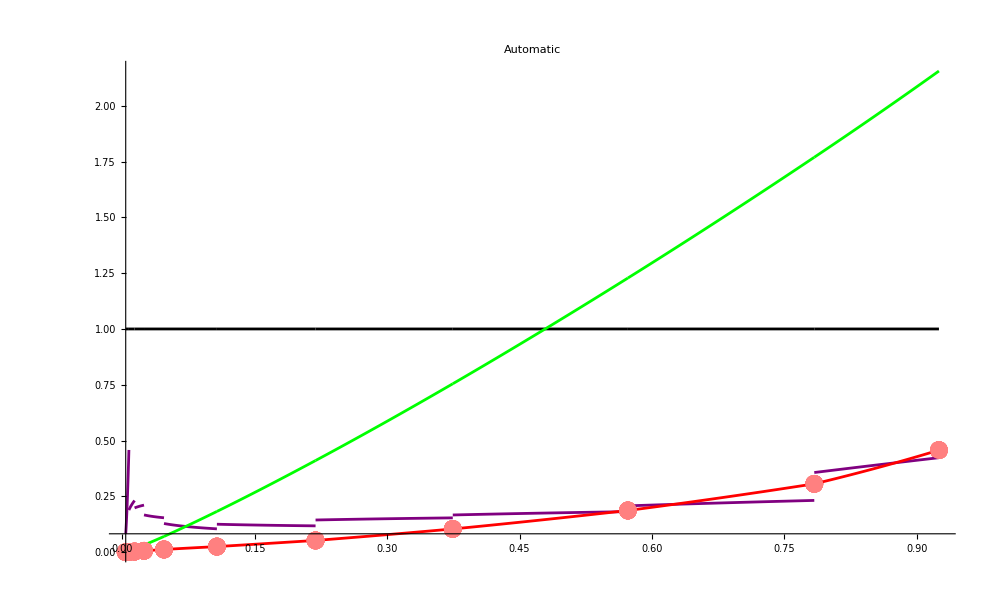

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];
AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,Parr},PlotStyle->Pink]];
]
Show[Plotlist,PlotRange->Automatic,PlotLabel->Automatic]
```

```mathematica
convmN4=101425.86;
```

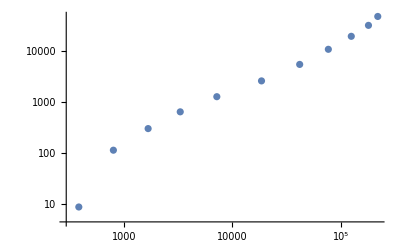

```mathematica
ListLogLogPlot[Table[{epsarr[[i]]*convmN4,Parr[[i]]*convmN4},{i,1,Length[Parr]}]]
```

```mathematica
epsarrout=epsarr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Parrout=Parr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Export[NotebookDirectory[]<>"output/heavy_points.dat",{epsarrout,Parrout}]
```

{382.607,797.22,1666.98,3296.89,7168.91,18516.,41648.6,76534.,124565.}

{8.69561,112.237,297.094,631.838,1249.86,2545.77,5347.33,10564.8,18962.3}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/heavy_points.dat